# QuantileRegression

Computes Quantile Regression fits over a time series, a list of numbers, or a list of numeric pairs.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
Clear[QuantileRegression];

SyntaxInformation[QuantileRegression]={"ArgumentsPattern"->{_.,_,_,OptionsPattern[]}};

QuantileRegression::"nmat"="The first argument is expected to be a matrix of numbers with two columns, a numeric vector, or a time series.";

QuantileRegression::"knord"="The specified knots `1` and interpolation order `2` produce no B-Spline basis functions. The expression n - i - 2 should be non-negative, where n is the number of knots and i is the interpolation order.";

QuantileRegression::"zerob"="The specified knots `1` and interpolation order `2` produced a list of zeroes instead of a list of B-Spline basis functions.";

QuantileRegression::"knspec"="The knots specification (for using B-splines) has to be an integer or a list of numbers.";

QuantileRegression::"nprobs"="The third argument is expected to be a list of numbers representing probabilities.";

QuantileRegression::"nmeth"="The value of the method option is expected to be LinearProgramming or a list with LinearProgramming as a first element.";

QuantileRegression::"norder"="The value of the option InterpolationOrder is expected to be a non-negative integer.";

QuantileRegression::"nargs"="Three arguments are expected.";

Options[QuantileRegression]={InterpolationOrder->3,Method->LinearProgramming};

QuantileRegression[data_?VectorQ,knots_,probs_,opts:OptionsPattern[]]:=QuantileRegression[Transpose[{Range[Length[data]],data}],knots,probs,opts];

QuantileRegression[data:(_TimeSeries|_TemporalData),knots_,probs_,opts:OptionsPattern[]]:=
QuantileRegression[QuantityMagnitude[data["Path"]],knots,probs,opts];

QuantileRegression[data_,knots_,probsArg_,opts:OptionsPattern[]]:=
Block[{mOptVal,intOrdOptVal,probs=Flatten@List@probsArg},

Which[
!(MatrixQ[data,NumericQ]&&Dimensions[data][[2]]≥2),
Message[QuantileRegression::"nmat"];Return[{}],

!(IntegerQ[knots]&&knots>0||VectorQ[knots,NumericQ]),
Message[QuantileRegression::"knspec"];Return[{}],

!VectorQ[probs,NumericQ[#]&&0≤#≤1&],
Message[QuantileRegression::"nprobs"];Return[{}]
];

mOptVal=OptionValue[QuantileRegression,Method];
intOrdOptVal=OptionValue[QuantileRegression,InterpolationOrder];

Which[
!(IntegerQ[intOrdOptVal]&&intOrdOptVal≥0),
Message[QuantileRegression::"norder"];Return[{}],

TrueQ[mOptVal===LinearProgramming],
LPSplineQuantileRegression[data,knots,intOrdOptVal,probs],

ListQ[mOptVal]&&TrueQ[mOptVal[[1]]===LinearProgramming],
LPSplineQuantileRegression[data,knots,intOrdOptVal,probs,Rest[mOptVal]],

True,
Message[QuantileRegression::"nmeth"];Return[{}]
]
];

QuantileRegression[___]:=Block[{},Message[QuantileRegression::"nargs"];
{}];

Clear[LPSplineQuantileRegression];

LPSplineQuantileRegression[data_?MatrixQ,npieces_Integer,order_Integer,probs:{_?NumberQ..},opts:OptionsPattern[]]:=LPSplineQuantileRegression[data,Rescale[Range[0,1,1/npieces],{0,1},{Min[data[[All,1]]],Max[data[[All,1]]]}],order,probs,opts];

LPSplineQuantileRegression[dataArg_?MatrixQ,knotsArg:{_?NumberQ..},order_Integer,probs:{_?NumberQ..},opts:OptionsPattern[]]:=Block[{data=dataArg,knots=Sort[knotsArg],yMedian=0,yFactor=1,yShift=0,n=Dimensions[dataArg][[1]],pfuncs,c,t,qrSolutions,mat},

If[Min[data[[All,2]]]<0,
yMedian=Median[data[[All,2]]];
yFactor=InterquartileRange[data[[All,2]]];
data[[All,2]]=Standardize[data[[All,2]],Median,InterquartileRange];
yShift=Abs[Min[data[[All,2]]]];
data[[All,2]]=data[[All,2]]+yShift;
];

(*Enhance the knots list with additional clamped knots.*)
knots=Join[Table[Min[knots],{order}],knots,Table[Max[knots],{order}]];
If[Length[knots]-order-2<0,Message[QuantileRegression::"knord",knots,order];
Return[{}]
];

(*B-spline basis expressions*)
pfuncs=Table[PiecewiseExpand[BSplineBasis[{order,knots},i,t]],{i,0,Length[knots]-order-2}];
If[VectorQ[pfuncs,#==0&],
Message[QuantileRegression::"zerob",knots,order];
Return[{}]
];

(*B-spline basis functions*)
pfuncs=Function[{f},With[{bf=f/.t->#},bf&]]/@pfuncs;

(*Create the conditions matrix*)
mat=Table[Join[Through[pfuncs[data[[i,1]]]]],{i,1,n}];
mat=MapThread[Join,{mat,IdentityMatrix[n],-IdentityMatrix[n]}];
mat=SparseArray[mat];

(*Find the regression quantiles*)
qrSolutions=
Table[
c=Join[ConstantArray[0,Length[pfuncs]],ConstantArray[1,n] q,ConstantArray[1,n] (1-q)];
t=LinearProgramming[c,mat,Transpose[{data[[All,2]],ConstantArray[0,n]}],DeleteCases[{opts},InterpolationOrder->_]];
If[!(VectorQ[t,NumberQ]&&Length[t]>Length[pfuncs]),ConstantArray[0,Length[pfuncs]],t],
{q,probs}];

If[yMedian==0&&yFactor==1,
Table[With[{f=pfuncs[[All,1]].qrSolutions[[i,1;;Length[pfuncs]]]},f&],{i,1,Length[probs]}],
(*ELSE*)
Map[Function[{ws},With[{f=yFactor ((pfuncs[[All,1]].ws)-yShift)+yMedian},f&]],qrSolutions[[All,1;;Length[pfuncs]]]]
]
];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

QuantileRegression[data,knots,probs]

does quantile regression over the times series or data array data using the knots specification knots for the probabilties probs .

QuantileRegression[data,knots,probs,opts]

does quantile regression with the options opts .

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

QuantileRegression works on time series, lists of numbers, and lists of numeric pairs.

The curves computed with quantile regression are called regression quantiles.

The regression quantiles corresponding to the specified probabilities are linear combinations of B-splines generated over the specified knots.

In other words, QuantileRegression computes fits using a B-spline functions basis. The basis is specified with the knots argument and the option InterpolationOrder.

QuantilesRegression takes the following options:

InterpolationOrder | 3 | interpolation order
Method | LinearProgramming | method for the quantile regression computations

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Make a random signal:

```mathematica
SeedRandom[23];
n=200;
randData=Transpose[{Range[n],RandomReal[{0,100.},n]}];
```

Compute Quantile Regression with 5 knots for the probabilities 0.25 and 0.75:

```mathematica
qFuncs=QuantileRegression[randData,5,{0.25,0.75}];
```

Here are the formulas of the obtained regression quantiles:

```mathematica
Simplify/@Through[qFuncs[x]]
```

{Piecewise[{{0., x>200||x<1}, {3818.78-70.5999 x+0.433163 x^2-0.000875772 x^3, 801/5<x≤200}, {4099.05-75.8484 x+0.465925 x^2-0.000943942 x^3, 5 x==801}, {84.2683-0.501637 x-0.00576232 x^2+0.0000412732 x^3, 403/5<x≤602/5}, {-62.9078+4.97638 x-0.0737278 x^2+0.000322355 x^3, 204/5≤x≤403/5}, {34.9017-2.21549 x+0.102544 x^2-0.00111777 x^3, 1≤x<204/5}, {110.681-1.15976 x-0.000296216 x^2+0.0000261401 x^3, True}}],Piecewise[{{0., x>200||x<1}, {506.187-14.1371 x+0.14281 x^2-0.000456464 x^3, 403/5≤x<602/5}, {983.69-15.2439 x+0.0846418 x^2-0.000155264 x^3, 801/5≤x≤200}, {59.6756+1.19519 x-0.0158668 x^2-0.0000579967 x^3, 1≤x<204/5}, {-759.529+17.4007 x-0.119132 x^2+0.000268735 x^3, 602/5≤x<801/5}, {24.2224+3.80204 x-0.0797601 x^2+0.000464008 x^3, True}}]}

Here is a plot of the original data and the obtained regression quantiles:

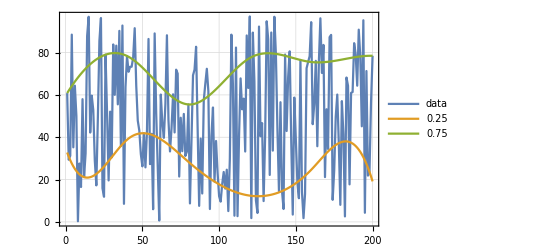

```mathematica
ListLinePlot[{randData,qFuncs⟦1⟧/@randData⟦All,1⟧,qFuncs⟦2⟧/@randData⟦All,1⟧},PlotLegends->{"data",0.25,0.75},PlotStyle->{Thin,Thick,Thick},PlotTheme->"Detailed"]
```

Find the fraction of the data points that are under the second regression quantile:

```mathematica
Length[Select[randData,#⟦2⟧<qFuncs⟦2⟧[#⟦1⟧]&]]/Length[randData]//N
```

0.75

The obtained fraction is close to the second probability, 0.75, given to QuantileRegression.

### Scope

Here is a Quantile Regression computation over a numerical vector:

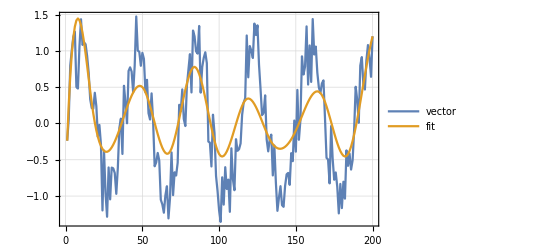

```mathematica
vecData=Sin[Range[200]/6]+RandomReal[{-0.5,0.5},200];
qFunc=First@QuantileRegression[vecData,12,0.5];
ListLinePlot[{vecData,qFunc[#]&/@Range[Length[vecData]]},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"vector","fit"}]
```

Here is a quantile regression computation over a times series object:

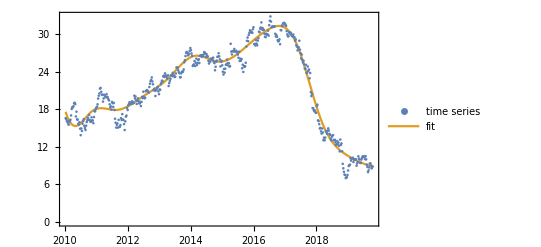

```mathematica
finData=FinancialData["GE",{{2010,1,1},{2019,10,15},"Week"}];
qFunc=First@QuantileRegression[finData,12,0.5];
DateListPlot[{finData,{#,qFunc[#]}&/@finData["Times"]},Joined->{False,True},PlotLegends->{"time series","fit"}]
```

The second argument -- the knots specification -- can be an integer specifying the number of knots, or a list of numbers specifying the knots of the B-spline basis:

```mathematica
qFuncs=QuantileRegression[randData,randData⟦1;;-1;;3,1⟧,0.5];
```

### Options

#### InterpolationOrder

The option InterpolationOrder specifies the polynomial order of the B-spline basis. Its values are expected to be non-negative integers:

```mathematica
qFuncs=Table[First@QuantileRegression[randData,5,0.5,InterpolationOrder->i],{i,{0,1,3}}];
```

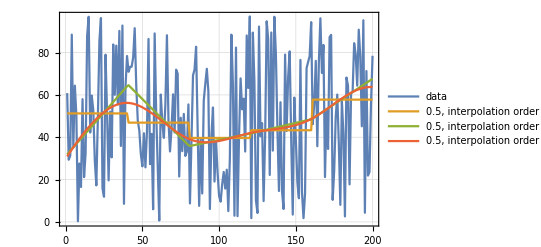

```mathematica
ListLinePlot[Prepend[(#1/@Range[Length[randData]]&)/@qFuncs,randData],PlotStyle->{Thin,Thick,Thick,Thick},PlotLegends->Prepend[{"0.5, interpolation order 0","0.5, interpolation order 1","0.5, interpolation order 3"},"data"],PlotTheme->"Detailed"]
```

#### Method

QuantileRegression uses LinearProgramming. Additional parameters can be passed to LinearProgramming with the Method option:

```mathematica
qFuncs=QuantileRegression[randData,5,0.5,Method->{LinearProgramming,Tolerance->10^(-2),Method->"CLP"}];
```

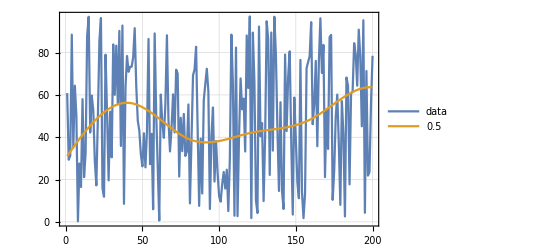

```mathematica
ListLinePlot[{randData,qFuncs⟦1⟧/@randData⟦All,1⟧},PlotStyle->{Thin,Thick},PlotLegends->{"data",0.5},PlotTheme->"Detailed"]
```

### Applications

#### Fit for heteroscedastic data

Here is heteroscedastic data (the variance is not constant with respect to the predictor variable):

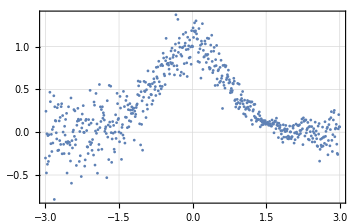

```mathematica
distData=Table[{x,Exp[-x^2]+RandomVariate[NormalDistribution[0,.15 √(Abs[1.5-x]/1.5)]]},{x,-3,3,.01}];
ListPlot[distData,PlotTheme->"Detailed",ImageSize->Medium]
```

Find quantile regression fits:

```mathematica
probs={0.1,0.25,0.5,0.75,0.9};
qFuncs=QuantileRegression[distData,4,probs];
```

Plot the data and the regression quantiles:

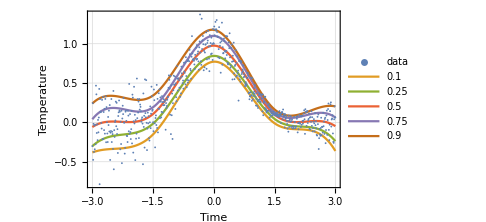

```mathematica
ListPlot[Prepend[(Transpose[{distData⟦All,1⟧,#1/@distData⟦All,1⟧}]&)/@qFuncs,distData],Joined->Prepend[Table[True,Length[probs]],False],PlotLegends->Prepend[probs,"data"],PlotTheme->"Detailed",FrameLabel->{"Time","Temperature"},ImageSize->Medium]
```

Note that the regression quantiles clearly outline the heteroscedastic nature of the data.

#### Fit and anomalies for financial time series

Here is a financial time series:

```mathematica
finData=FinancialData["GE",{{2016,1,1},{2019,10,15},"Day"}]
```

TimeSeries[…]

```mathematica
finData//Head
```

TemporalData

Do a quantile regression fit and plot it:

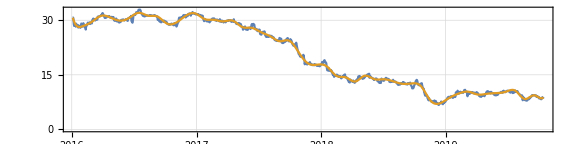

```mathematica
qFunc=First@QuantileRegression[finData,50,0.5];
DateListPlot[{finData,{#,qFunc[#]}&/@finData["Times"]},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Large,PlotLegends->{"data","fit"}]
```

Here are the errors of the found fit:

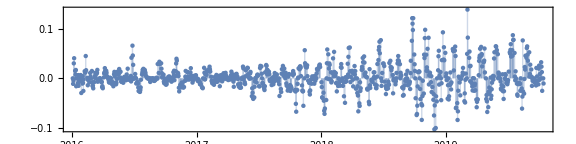

```mathematica
DateListPlot[Map[{#⟦1⟧,(qFunc[#⟦1⟧]-#⟦2⟧)/#⟦2⟧}&,QuantityMagnitude[finData["Path"]]],Joined->False,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Large]
```

Find anomalies positions in the list of fit errors:

```mathematica
pos=FindAnomalies[Map[(qFunc[#⟦1⟧]-#⟦2⟧)/#⟦2⟧&,QuantityMagnitude[finData["Path"]]],"AnomalyPositions"]
```

{688,689,690,691,716,734,736,750,798}

Plot the data, fit, and anomalies:

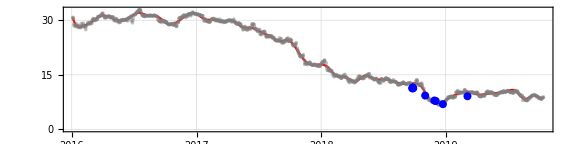

```mathematica
DateListPlot[{finData,{#,qFunc[#]}&/@finData["Times"],finData["Path"]⟦pos⟧},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Large,Joined->{False,True,False},PlotStyle->{{GrayLevel[0.5],Opacity[0.5]},{Red,Thick},{Blue,PointSize[0.01]}},PlotLegends->{"data","fit","anomalies"}]
```

#### Analyze temperature time series

Get temperature data:

```mathematica
tempData=WeatherData[{"Orlando","Florida","USA"},"Temperature",{{2016,1,1},{2019,1,1},"Day"}]
```

TimeSeries[…]

Convert the time series into a list of numeric pairs:

```mathematica
tempData=QuantityMagnitude[tempData["Path"]];
```

Compute quantile regression fits:

```mathematica
probs=Sort[Join[Range[0.1,0.9,0.1],{0.01,0.99}]];
qFuncs=QuantileRegression[tempData,10,probs];
```

Plot the data and the regression quantiles:

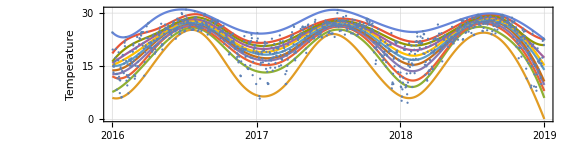

```mathematica
DateListPlot[Prepend[(Transpose[{tempData⟦All,1⟧,#1/@tempData⟦All,1⟧}]&)/@qFuncs,tempData],Joined->Prepend[Table[True,Length[probs]],False],PlotLegends->Prepend[probs,"temperature data"],AspectRatio->1/4,PlotTheme->"Detailed",FrameLabel->{"Time","Temperature"},ImageSize->Large]
```

Find an estimate of the conditional Cumulative Distribution Function (CDF) at the date 2017-10-01:

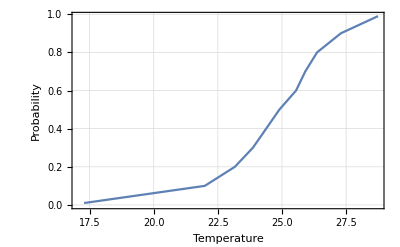

```mathematica
ListLinePlot[Transpose[{Through[qFuncs[AbsoluteTime[{2017,10,1}]]],probs}],]
```

Find outliers in the temperature data -- we define outliers as points below or above the 0.02 and 0.98 regression quantiles respectively:

```mathematica
qFuncs=QuantileRegression[tempData,10,{0.02,0.98}];
```

```mathematica
bottomOutliers=Select[tempData,#⟦2⟧<qFuncs⟦1⟧[#⟦1⟧]&];
topOutliers=Select[tempData,#⟦2⟧>qFuncs⟦-1⟧[#⟦1⟧]&];
```

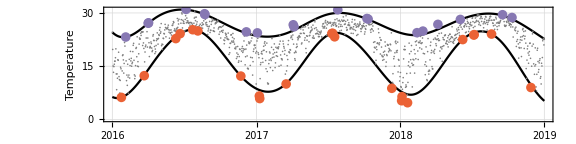

```mathematica
DateListPlot[{tempData,{#,qFuncs⟦1⟧[#]}&/@tempData⟦All,1⟧,{#,qFuncs⟦-1⟧[#]}&/@tempData⟦All,1⟧,bottomOutliers,topOutliers},]
```

### Properties and Relations

QuantileRegression can be compared with FindFormula, Fit , LinearModelFit, and NonlinearModelFit:

```mathematica
qFunc=First@QuantileRegression[distData,4,0.5];
```

```mathematica
fFunc=LinearModelFit[distData,Table[x^i,{i,0,5,1}],x]["Function"];
```

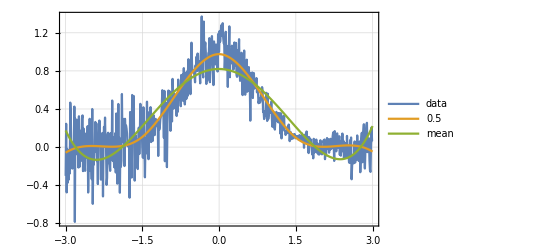

```mathematica
ListLinePlot[{distData,{#,qFunc[#]}&/@distData⟦All,1⟧,{#,fFunc[#]}&/@distData⟦All,1⟧},PlotStyle->{Thin,Thick,Thick},PlotLegends->{"data",0.5,"mean"},PlotTheme->"Detailed"]
```

### Possible Issues

#### Slow computations

Because of the Linear Programming formulation for some data and knots specifications the computations can be slow.

#### Fitting for probabilities 0 and 1

For most data the quantile regression fitting for probabilities 0 and 1 produces regression quantiles that “too far away from the data.”

Find regression quantiles for probabilities 0 and 0.5 and plot them:

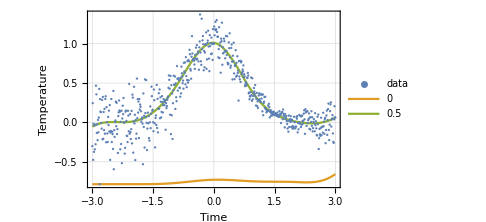

```mathematica
probs={0,0.5};
qFuncs=QuantileRegression[distData,6,probs];
ListPlot[Prepend[(Transpose[{distData⟦All,1⟧,#1/@distData⟦All,1⟧}]&)/@qFuncs,distData],Joined->Prepend[Table[True,Length[probs]],False],PlotLegends->Prepend[probs,"data"],PlotTheme->"Detailed",FrameLabel->{"Time","Temperature"},ImageSize->Medium]
```

Find regression quantiles for probabilities 0.5, and 1 and plot them:

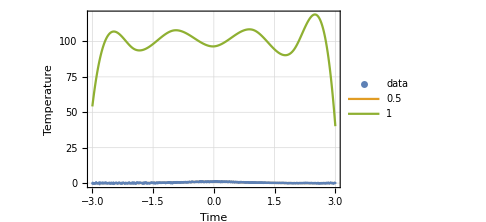

```mathematica
probs={0.5,1};
qFuncs=QuantileRegression[distData,6,probs];
ListPlot[Prepend[(Transpose[{distData⟦All,1⟧,#1/@distData⟦All,1⟧}]&)/@qFuncs,distData],Joined->Prepend[Table[True,Length[probs]],False],PlotLegends->Prepend[probs,"data"],PlotTheme->"Detailed",FrameLabel->{"Time","Temperature"},ImageSize->Medium]
```

One way to fix this is to use probabilities that are close to 0 and 1 from above and below respectively:

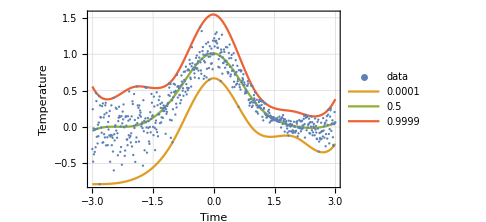

```mathematica
probs={0.0001,0.5,0.9999};
qFuncs=QuantileRegression[distData,6,probs];
ListPlot[Prepend[(Transpose[{distData⟦All,1⟧,#1/@distData⟦All,1⟧}]&)/@qFuncs,distData],Joined->Prepend[Table[True,Length[probs]],False],PlotLegends->Prepend[probs,"data"],PlotTheme->"Detailed",FrameLabel->{"Time","Temperature"},ImageSize->Medium]
```

#### Over-fitting

Consider the following non-linear data:

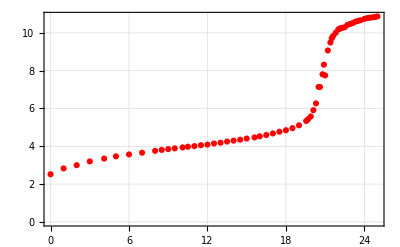

```mathematica
nlData={};
ListPlot[nlData,]
```

Make a quantile regression fit with 20 knots:

```mathematica
qFunc20=First@QuantileRegression[nlData,20,{0.5},InterpolationOrder->2];
```

Make a quantile regression fit with 40 knots:

```mathematica
qFunc40=First@QuantileRegression[nlData,40,{0.5},InterpolationOrder->2];
```

Plot the regression quantiles and the data:

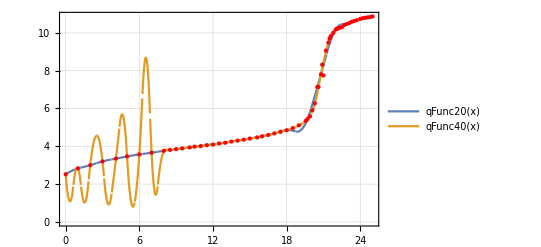

```mathematica
Plot[{qFunc20[x],qFunc40[x]},{x,Min[nlData⟦All,1⟧],Max[nlData⟦All,1⟧]},Epilog->{Red,Point[nlData]},PlotTheme->"Detailed"]
```

We can see that the regression quantile computed with 40 knots is “over-fitted” between 0 and 8 -- the B-spline basis knots are too densely placed between 0 and 8.

#### Intersecting regression quantiles

When regression quantiles are over-fitted then the estimate of the conditional Cumulative Distribution Function (CDF) can be problematic -- the estimated CDF is not a monotonically increasing function.

Compute regression quantiles using “too many” knots:

```mathematica
probs=Sort[Join[Range[0.1,0.9,0.1],{0.01,0.99}]];
qFuncs=QuantileRegression[tempData,30,probs];
```

Plot the regression quantiles:

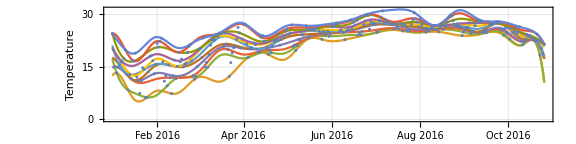

```mathematica
Block[{data=tempData⟦1;;300⟧},qFuncs=QuantileRegression[data,20,probs];DateListPlot[Prepend[(Transpose[{data⟦All,1⟧,#1/@data⟦All,1⟧}]&)/@qFuncs,data],Joined->Prepend[Table[True,Length[probs]],False],PlotLegends->Prepend[probs,"temperature data"],AspectRatio->1/4,PlotTheme->"Detailed",FrameLabel->{"Time","Temperature"},ImageSize->Large]]
```

Here is the estimated conditional CDF:

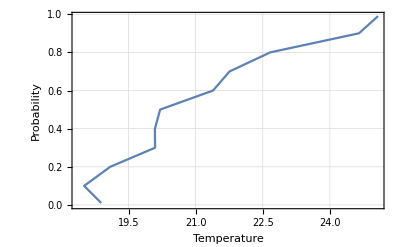

```mathematica
ListLinePlot[Transpose[{Through[qFuncs[tempData⟦100,1⟧]],probs}],PlotTheme->"Detailed",FrameLabel->{"Temperature","Probability"}]
```

#### Rescaling

For certain data it is beneficial to rescale the predictor values, predicted values, or both before doing the quantile regression computations:

```mathematica
finData2=N@{10532750,1342440,714972,1289802,1302765,814231,830680,416649,80017,24343,1808,1939,25848,32532,21807,26108,12581,36315,34544,3827,7631,7259};
```

```mathematica
QuantileRegression[finData2,4,probs]
```

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming::lpsnf will be suppressed during this calculation.

{0&,0&,0&,0&,0&,0&,0&,0&,0&,0&,0&}

```mathematica
qFuncs=QuantileRegression[Rescale[finData2],4,probs];
Through[qFuncs[10]]
```

{0.000157877,0.000191528,0.00213988,0.00532975,0.0242553,0.0227434,0.0443625,0.0434907,0.0322355,0.0322355,0.0322355}

### Neat Examples

Compute and plot regression quantiles over symmetric data:

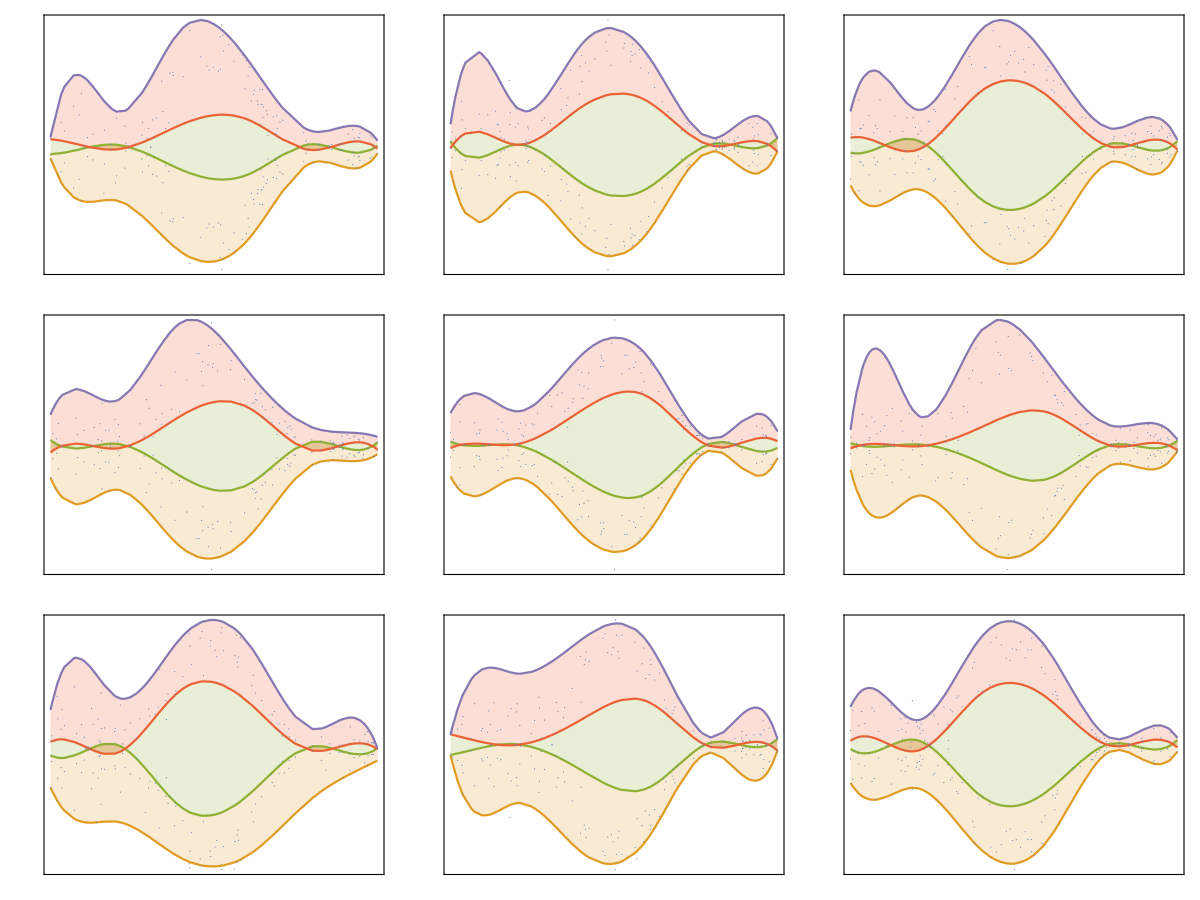

```mathematica
SeedRandom[20];
distData=Table[{x,Exp[-x^2]+RandomVariate[NormalDistribution[0,.15 √(Abs[1.5-x]/1.5)]]},{x,-3,3,.01}];
Grid[Table[Block[{tempData=RandomSample[distData,100],data,probs},
data=Join[tempData,{#⟦1⟧,-#⟦2⟧}&/@tempData];
data=SortBy[Transpose[Rescale/@Transpose[data]],#⟦1⟧&];
probs={0.02,0.48,0.52,0.98};
qFuncs=QuantileRegression[data,5,probs,Method->{LinearProgramming,Method->"InteriorPoint",Tolerance->10^(-2)}];ListPlot[Prepend[(Transpose[{data⟦All,1⟧,#1/@data⟦All,1⟧}]&)/@qFuncs,data],Joined->Prepend[Table[True,Length[probs]],False],Filling->Prepend[Table[(i+1)->{i+2},{i,Length[probs]-1}],1->None],Frame->True,FrameTicks->False,Axes->False,ImageSize->Small,AspectRatio->1]
],3,3]]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Anomalies

Outliers

Regression

Quantile Regression

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

BSplineBasis

FindFormula

Fit

LinearModelFit

LinearProgramming

NonlinearModelFit

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Anton Antonov, Quantile regression through linear programming, (2013), MathematicaForPrediction at WordPress.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://mathematicaforprediction.wordpress.com/2013/12/16/quantile-regression-through-linear-programming/

https://mathematicaforprediction.wordpress.com/2014/01/01/quantile-regression-with-b-splines

https://github.com/antononcube/MathematicaForPrediction/blob/master/QuantileRegression.m

https://mathematicaforprediction.wordpress.com/2018/08/01/a-monad-for-quantile-regression-workflows/

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

#### Data

```mathematica
distData=Table[{x,Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]]},{x,-3,3,.2}];
```

```mathematica
distData2=Table[{x,Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]]},{x,-3,3,.01}];
```

```mathematica
finData=FinancialData["GE",{{2018,1,1},{2019,10,15},"Month"}];
```

#### These should pass

```mathematica
probs=Range[0.2,0.8,0.2];
```

```mathematica
qFuncs=QuantileRegression[distData,12,probs];
ListQ[qFuncs]&&Length[qFuncs]==Length[probs]&&Apply[And,TrueQ[Head[#]===Function]&/@qFuncs]
```

True

```mathematica
VectorQ[Through[qFuncs[0]],NumberQ]
```

True

```mathematica
qFuncs=QuantileRegression[distData,{-3,-2,1,0,1,1.5,2.5,3},probs];
ListQ[qFuncs]&&Length[qFuncs]==Length[probs]&&Apply[And,TrueQ[Head[#]===Function]&/@qFuncs]
```

True

```mathematica
qFuncs=QuantileRegression[distData,{-3,-2,1,0,1,1.5,2.5,3},0.5];
ListQ[qFuncs]&&Length[qFuncs]==1&&Apply[And,TrueQ[Head[#]===Function]&/@qFuncs]
```

True

```mathematica
qFuncs=QuantileRegression[distData[[All,2]],12,probs];
ListQ[qFuncs]&&Length[qFuncs]==Length[probs]&&Apply[And,TrueQ[Head[#]===Function]&/@qFuncs]
```

True

```mathematica
qFuncs=QuantileRegression[finData,12,probs];
ListQ[qFuncs]&&Length[qFuncs]==Length[probs]&&Apply[And,TrueQ[Head[#]===Function]&/@qFuncs]
```

True

```mathematica
qFuncs=QuantileRegression[distData2,6,probs];
sepPointsFractions=Map[Function[{f},Length[Select[distData2,#⟦2⟧<f[#⟦1⟧]&]]/Length[distData2]//N],qFuncs];
Norm[sepPointsFractions-probs,∞]<=0.01
```

True

#### These should fail

```mathematica
QuantileRegression[BlahBlah,43,0.3]
```

QuantileRegression::nmat: The first argument is expected to be a matrix of numbers with two columns, a numeric vector, or a time series.

{}

```mathematica
QuantileRegression[finData,0,0.3]
```

QuantileRegression::knspec: The knots specification (for using B-splines) has to be an integer or a list of numbers.

{}

```mathematica
QuantileRegression[finData,12.2,0.3]
```

QuantileRegression::knspec: The knots specification (for using B-splines) has to be an integer or a list of numbers.

{}

```mathematica
QuantileRegression[finData,12,BlahBlah]
```

QuantileRegression::nprobs: The third argument is expected to be a list of numbers representing probabilities.

{}

```mathematica
QuantileRegression[finData,12,23]
```

QuantileRegression::nprobs: The third argument is expected to be a list of numbers representing probabilities.

{}

```mathematica
QuantileRegression[finData,12,0.5,InterpolationOrder->2.6]
```

QuantileRegression::norder: The value of the option InterpolationOrder is expected to be a non-negative integer.

{}

```mathematica
QuantileRegression[finData,12,0.5,Method->BlahBlah]
```

QuantileRegression::nmeth: The value of the method option is expected to be LinearProgramming or a list with LinearProgramming as a first element.

{}

## Author Notes

The workflows described above are simplified and streamlined with the software monad QRMon.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

The tests above are based on the unit tests for the implementation of QuantileRegression at GitHub: https://github.com/antononcube/MathematicaForPrediction/blob/master/UnitTests/QuantileRegression-Unit-Tests.mt .